```mathematica
Clear[Lx, Ly, A, l, mL,
 SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
 Cons]
```

```mathematica
Lx = 32;
Ly = 32;
l = Ly/2;
mL = Lx/2;
A = Lx*Ly + Ly-l
NOrbitals = 2*A;
```

1040

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DSingDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DSingDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{SX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=I/2, SX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=-I/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DSingDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DSingDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{CX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=1/2, CX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=1/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
SY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{SY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=I/2, SY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = -I/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{SY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=I/2, SY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = -I/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{SY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=I/2, SY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = -I/2},{a,1,mL }]
Do[{SY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=I/2, SY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = -I/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{CY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=1/2, CY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = 1/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{CY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=1/2, CY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = 1/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{CY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=1/2, CY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = 1/2},{a,1,mL }]
Do[{CY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=1/2, CY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = 1/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHIDisloc]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHIDisloc[t_,t0_,m_]:=t*(KroneckerProduct[SX2DSingDis,σ1]+KroneckerProduct[SY2DSingDis, σ2])+KroneckerProduct[m*Cons-t0*(CX2DSingDis+CY2DSingDis),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHIDisloc[1.0,1.0,1.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

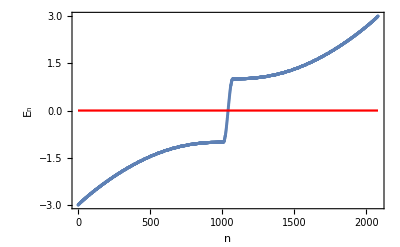

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(**---------------------------------------------------------**)
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{32,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l+1},{mL+1,Ly}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{16,2,2}

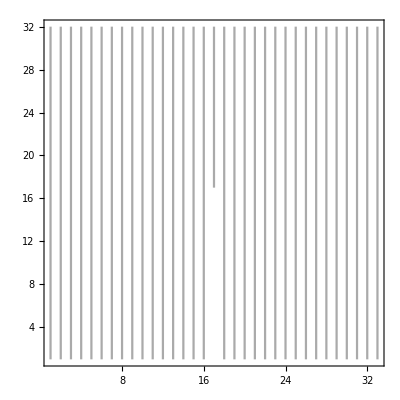

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},
Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,Round[Ly/4]+1,Round[3 Ly/4],Ly},None},{{1,Round[Lx/2]+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]]
```

-Graphics-

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

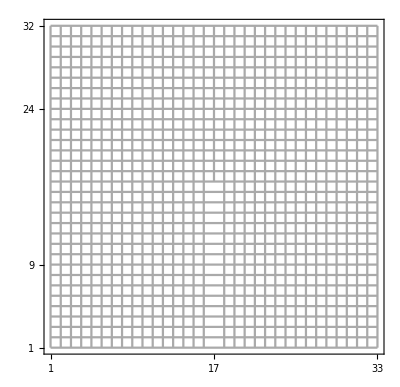

```mathematica
P5=Show[P2B,P3,P4]
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
LineUp[x_]:=(2/(1+Sqrt[5]))*(x-1)+8
LineDn[x_]:=(2/(1+Sqrt[5]))*(x-2)+6
```

```mathematica
N[LineUp[6]]
```

11.0902

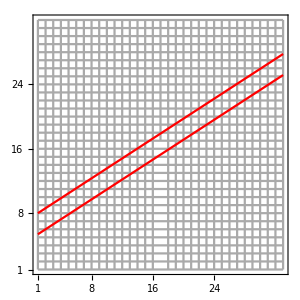

```mathematica
Show[P5,
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(**---This function generates site number for a given coordinates and set of parameter---**)
```

```mathematica
(**---Generates 0 for non existing points, e.g. the two lines below and above dislocation centers---**)
```

```mathematica
GenerateSiteNumber[x_,y_,Lx_,Ly_,l_,mL_]:=Piecewise[{{x+(y-1)Lx, 1≤ x ≤ mL &&1≤ y≤ l },{x+(y-1)Lx-1, Lx+1≥ x > mL+1 &&1≤ y≤ l},{x+(y-1)(Lx+1)-l,l<y≤Ly&&Lx+1≥ x ≥ 1 }},0]
```

```mathematica
(** Dislocation center site number **)
```

```mathematica
GenerateSiteNumber[15,15,Lx,Ly,l,mL]
```

463

```mathematica
28*14+15
```

407

```mathematica
Clear[FibonListNew]
FibonListNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
(**--x runs from 1 to Lx + 1--**)
```

```mathematica
Do[Do[FibonListNew=Append[FibonListNew,GenerateSiteNumber[x,y,Lx,Ly,l,mL]],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx+1}]
```

```mathematica
FibonList=Sort[FibonListNew]
```

{0,161,193,194,195,226,227,228,229,259,260,261,262,293,294,295,296,326,327,328,329,330,360,361,362,363,394,395,396,397,427,428,429,430,461,462,463,464,494,495,496,497,528,529,530,531,563,564,565,566,597,598,599,600,601,632,633,634,635,667,668,669,670,701,702,703,704,736,737,738,739,770,771,772,773,774,805,806,807,808,840,841,842,874,875}

```mathematica
(**--Delete the zeros, which are generated for the non-existing lines of atoms--**)
```

```mathematica
FibonList=DeleteCases[FibonList,0]
```

{161,193,194,195,226,227,228,229,259,260,261,262,293,294,295,296,326,327,328,329,330,360,361,362,363,394,395,396,397,427,428,429,430,461,462,463,464,494,495,496,497,528,529,530,531,563,564,565,566,597,598,599,600,601,632,633,634,635,667,668,669,670,701,702,703,704,736,737,738,739,770,771,772,773,774,805,806,807,808,840,841,842,874,875}

```mathematica
(** Dislocation center is in 108th position --- orbitals are 215 and 216 **)
```

```mathematica
Dimensions[FibonList]
```

{84}

```mathematica
Clear[Fibonup, Fibondown, TotalFibon]
```

```mathematica
Fibonup = 2 * FibonList -1;
```

```mathematica
Fibondown = 2* FibonList;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon=Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

168

```mathematica
NOrbitalsQuasi/2
```

84

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1880

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2080}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Dimensions[a]
```

{1912}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHIDisloc[1.,1.,-1];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

```mathematica
(** Make dislocation modes red **)
```

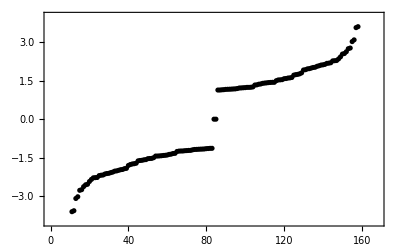

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
ValFibon;
```

```mathematica
(** Export["m+1DislocationRationalEnergies.dat",ValFibon]; **)
```

```mathematica
highestEnergy=ValFibon[[NOrbitalsQuasi/2]]
```

{84,-7.50233×10^-8}

```mathematica
PercentageOfSitesInside=N[(NOrbitalsQuasi/(2*A))*100]
```

8.07692

```mathematica
NOrbitalsQuasi
```

168

```mathematica
(**------------Plot probability density as a function of orbital number--------------**)
```

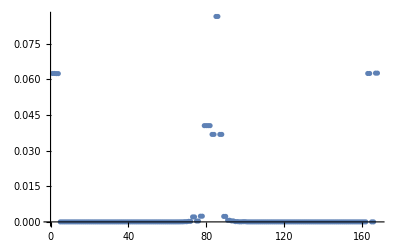

{Highest density at,{{86}}}

```mathematica
vecIndex=NOrbitalsQuasi/2+1;
ListPlot[Abs[ValVecFibon[[vecIndex]][[2]]]* Abs[ValVecFibon[[vecIndex]][[2]]]/Sum[Abs[ValVecFibon[[vecIndex]][[2]][[i]]]* Abs[ValVecFibon[[vecIndex]][[2]][[i]]],{i,1,NOrbitalsQuasi}],PlotRange->All]
{"Highest density at",Position[Abs[ValVecFibon[[vecIndex]][[2]]],Max[Abs[ValVecFibon[[vecIndex]][[2]]]]]}
```

```mathematica
NormaLizedState=Normalize[ValVecFibon[[vecIndex]][[2]]];
```

```mathematica
Dimensions[NormaLizedState]
```

{168}

```mathematica
ListPlot[Abs[NormaLizedState]*Abs[NormaLizedState],PlotRange->All]
```

-Graphics-

```mathematica
(**---Now we would plot it back, in a matrix (MatrixOfDensity) whose columns are x, y, sitenumber, density---**)
```

```mathematica
(Lx+1)Ly
```

1056

```mathematica
MatrixOfDensity = Table[{0,0,0,0},{i,1,(Lx+1)Ly}];
```

```mathematica
Do[Do[MatrixOfDensity[[j + (i-1)*Ly]]={i,j,GenerateSiteNumber[i,j,Lx,Ly,l,mL],0},{i,1,Lx+1}],{j,1,Ly}];
```

```mathematica
Dimensions[FibonList][[1]]
```

84

```mathematica
(** For i = 1 to Ly(Lx+1), if sitenumber matches some site in quasicrystal (which are in Fibonlist), copy density to MatrixDensity **)
```

```mathematica
Do[Do[ If[FibonList[[j]]==MatrixOfDensity[[i,3]],MatrixOfDensity[[i,4]]=Abs[NormaLizedState[[2*j-1]]]^2 +Abs[NormaLizedState[[2*j]]]^2 ,{}] ,{i,1,(Lx+1)Ly}],{j,1,NOrbitalsQuasi/2}]
```

```mathematica
Clear[datdislocation,colorfunc,rng,P1,P2,P2A,P2B,P2C,P3,P4,FilteredData]
```

```mathematica
datdislocation= Table[{0,0,0},{i,1,(Lx+1)Ly}];
```

```mathematica
(** We don't need the third column of MatrixDensity to actually plot, so we remove it **)
```

```mathematica
Do[{datdislocation[[i,1]]=MatrixOfDensity[[i,1]],datdislocation[[i,2]]=MatrixOfDensity[[i,2]] ,datdislocation[[i,3]]=MatrixOfDensity[[i,4]]},{i,1,(Lx+1)Ly}];
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]];*)
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];*)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,0.8]];
```

```mathematica
rng={0,Max[#]}&@datdislocation[[All,3]]
```

{0,0.172955}

```mathematica
Dimensions[datdislocation]
```

{1056,3}

```mathematica
FilteredData=Select[datdislocation,#[[3]]>0.005&];
```

```mathematica
Dimensions[FilteredData]
```

{9,3}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.8"},{rng[[2]]-10^-3,"1.6"}}]
```

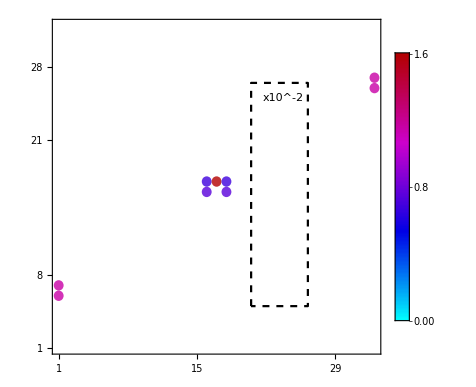

```mathematica
P2=Show[Graphics[{
PointSize[0.0001],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@FilteredData,

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2+1,29},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}},

Epilog-> {Inset[P1,{23.5,14}],Inset["x10^-2",{23.75,25}]}],
ListPlot[{{20.5,5},{20.5,26.5},{26.25,26.5},{26.25,5},{20.5,5}},Joined-> True,PlotStyle-> {Black,Dashed}]
]
```

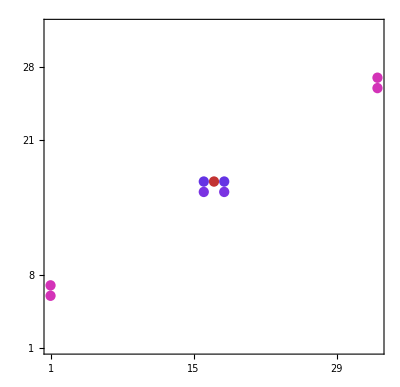

```mathematica
P2A=Show[Graphics[{
PointSize[0.04],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@FilteredData,


Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2+1,29},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]]
```

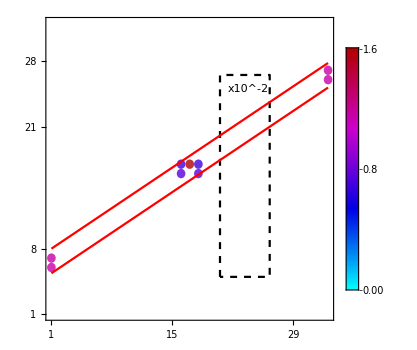

```mathematica
P2C=Show[P2,
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 350,AspectRatio-> 1
]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{32,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,28}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l+1},{mL+1,Ly}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{16,2,2}

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,14}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,13}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2+1,29},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

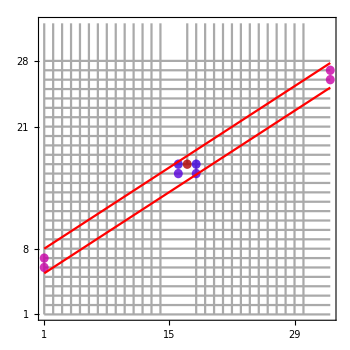

```mathematica
Show[P2B,P3,P4,P2A,
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 350,AspectRatio-> 1]
```

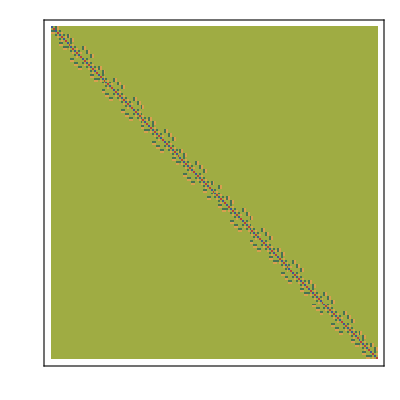

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

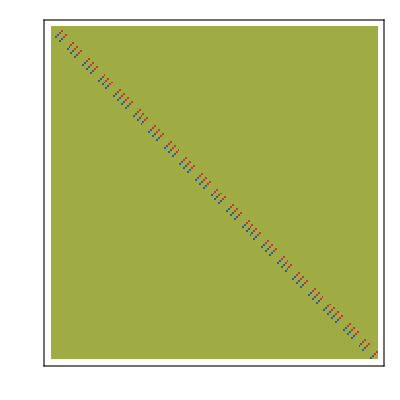

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

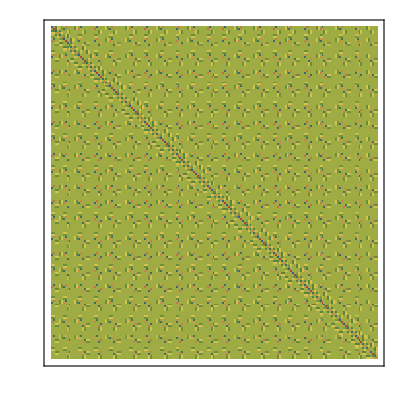

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

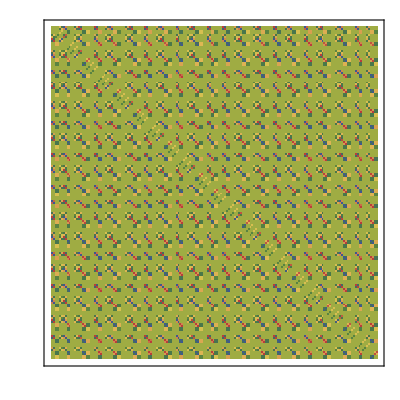

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
Dimensions[Fibon1D]
```

{85,2}

```mathematica
{133,2}
```

{133,2}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

63

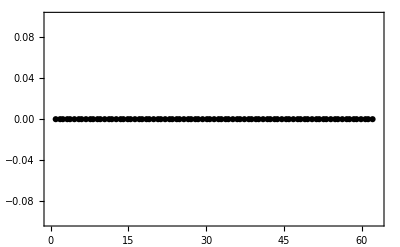

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

7.50233×10^-8

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2
},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfuncBW,rng,P1]
```

```mathematica
(** Blue **)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.2*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
(** Black and White **)
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@TabFibonacci[[All,3]]
```

{0,0.172955}

```mathematica
rng = {0,0.24}
```

{0,0.24}

```mathematica
rng[[2]]
```

0.24

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.12"},{rng[[2]]-10^-3,"0.24"}}]
```

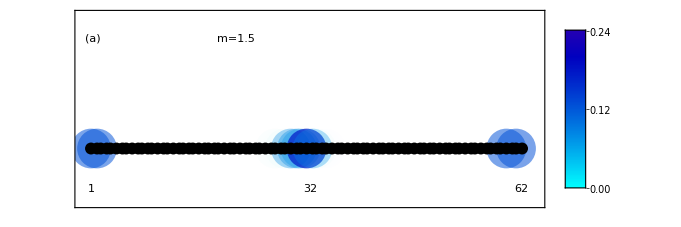

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

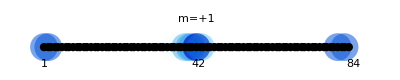

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
BaseStyle-> 18,
PlotRange-> {{-0.5,largestX+2},{-4.5,7}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
Epilog-> {Inset[1,{1,-3}],Inset[Ceiling[NOrbitalsQuasi/4],{Ceiling[largestX/2],-3}],Inset[NOrbitalsQuasi/2,{largestX,-3}],Inset["m=+1",{largestX/2,5}]
}
]
```